## Юрьев В. А. ПО-4 Лабораторная работа №5

# Задание 1

Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+   7
```

9

```mathematica
2/3
```

2/3

Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3      /7
```

3/7

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.          ^(1/2)
```

4.12311

Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
3                   (6 +  5 )
```

33

# Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[e^(x *Sqrt[163]), 40]
```

e^(12.76714533480370466171095200978089234738 x)

Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E, 100]
N[E^Pi, 100]
```

22.45915771836104547342715220454373502758931513399669224920300255406692604039911791231851975272714303

23.14069263277926900572908636794854738026610624260021199344504640952434235069045278351697199706754922

## Задание 3

Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумать свою

```mathematica
NSolve[{(4 x^3+y^4+5 y)/(y^4-5y)==4, x^5 y+y^5+x^5== 65}, {x,y}]
{{x->-0.9314439559259007-2.3294094016829323 ⅈ,y->-1.646260526941989-0.3453113142601871 ⅈ},{x->-0.9314439559259007+2.329409401682932 ⅈ,y->-1.646260526941989+0.34531131426018724 ⅈ},{x->0.20385145409165065+2.2923070077505523 ⅈ,y->-1.1579623411100637-2.1682364046298135 ⅈ},{x->0.20385145409165084-2.2923070077505523 ⅈ,y->-1.1579623411100635+2.1682364046298135 ⅈ},{x->-1.36473935086817+1.7726089329963568 ⅈ,y->-0.6807198562926658+2.126508388380639 ⅈ},{x->-1.364739350868169-1.7726089329963575 ⅈ,y->-0.6807198562926655-2.1265083883806386 ⅈ},{x->2.0270308298158537-0.8369080309558654 ⅈ,y->-1.3673662093223107+0.9586209026723267 ⅈ},{x->2.0270308298158537+0.8369080309558655 ⅈ,y->-1.3673662093223107-0.9586209026723268 ⅈ},{x->1.028980410016614+1.8888429154725468 ⅈ,y->-1.4118944875250727+1.8368455912543957 ⅈ},{x->1.028980410016614-1.8888429154725472 ⅈ,y->-1.4118944875250734-1.8368455912543953 ⅈ},{x->2.0394408686577004-0.5394888338554034 ⅈ,y->-0.2842141468342919+1.677858630046858 ⅈ},{x->2.0394408686577+0.5394888338554031 ⅈ,y->-0.28421414683429197-1.6778586300468583 ⅈ},{x->-1.815508083300875-0.9474402056827296 ⅈ,y->0.3020434378901156+1.1548558999660061 ⅈ},{x->-1.8155080833008752+0.9474402056827294 ⅈ,y->0.30204343789011595-1.154855899966006 ⅈ},{x->-1.8960377531468076+0.7388892196240249 ⅈ,y->-1.3788907164459003-1.4734243967993779 ⅈ},{x->-1.8960377531468073-0.7388892196240249 ⅈ,y->-1.3788907164459006+1.4734243967993774 ⅈ},{x->1.4152316056366274,y->2.160361484673415},{x->-1.1145165441621903-1.019375357702901 ⅈ,y->2.141089359271505-0.11855891889196617 ⅈ},{x->-1.1145165441621905+1.0193753577029012 ⅈ,y->2.1410893592715046+0.11855891889196633 ⅈ},{x->0.7457332935006381+1.858208984135536 ⅈ,y->0.9798584243131427+0.688080043803001 ⅈ},{x->0.7457332935006384-1.8582089841355358 ⅈ,y->0.9798584243131431-0.6880800438030008 ⅈ},{x->0.36959302850317294-1.7150735584990144 ⅈ,y->1.924136320660823+0.2971654978917703 ⅈ},{x->0.369593028503173+1.7150735584990144 ⅈ,y->1.9241363206608229-0.29716549789177044 ⅈ}}
```

## Задание 4

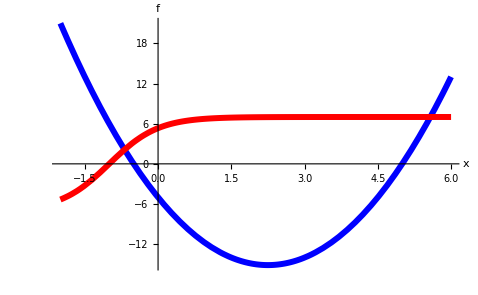
```mathematica
FindRoot[2 x^2-9 x - 5 == 7 Tanh[x+1], {x, -2,6}]
{x->5.57603163089452}
Plot[{2 x^2-9 x-5,7 Tanh[x+1]},{x,-2,6},PlotStyle->{{Thickness[0.009],RGBColor[0,0,1]},{Thickness[0.009],RGBColor[1,0,0]}},AxesLabel->{"x","f"}]
-Graphics-
```

# Задание 5

```mathematica
sol1=NDSolve[{y''[x]+3*x*y'[x]+(4 x^2+3)y[x]==0, y[0]==-1, y'[0]==2},y, {x,-2,3}]
{{y->InterpolatingFunction[…]}}
```

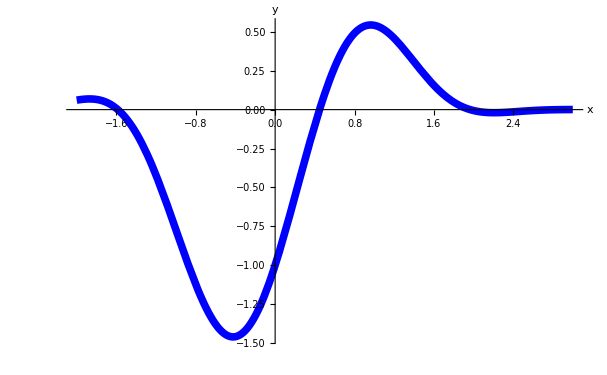
```mathematica
Plot[y[x]/.sol1, {x,-2,3}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
-Graphics-
```

```mathematica
(*a*)
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,-1.6}]
{x->-1.5858489208490636}
```

```mathematica
(*б*)
```

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2 (*minimum*)
```

```mathematica
(-0.5538101215152087)
```

```mathematica
sol3 = FindRoot[D[y[x]/.sol1[[1]],x]==0, {x,-1.6}] (*maximum*)
{x->-1.870545119084836}
```

```mathematica
(*в*)
```

```mathematica
y[x]/.sol1[[1]]/.sol3
0.06870300917047306
```

```mathematica
(*г*)
```

```mathematica
FindMaximum[y[x]/.sol1[[1]], {x,-1.6}]
{0.06870300917047295,{x->-1.8705451332361915}}
```

## Задание 6

```mathematica
task1 = Table[{x,(32+42x+83 x^2+87 x^3+93 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
{{0.,29.280965867403246},{0.25,54.59115095312549},{0.5,80.52015211305564},{0.75,201.97616796619056},{1.,274.1763745494385},{1.25,554.4536368376108},{1.5,953.1984354246163},{1.75,1815.2983841624643},{2.,2816.280567695984},{2.25,4408.4958610002905},{2.5,5503.550056534385},{2.75,7714.54648283271},{3.,12404.618089949308},{3.25,13605.357596552698},{3.5,15228.350169603287},{3.75,25867.649900980006},{4.,25429.30486948583},{4.25,34337.48425283154},{4.5,39308.8392764597},{4.75,59458.85715064692},{5.,68445.2320566609}}
```

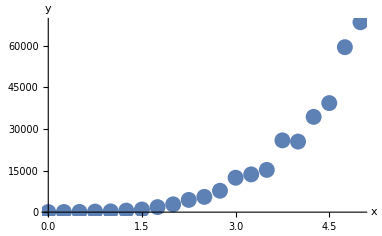
```mathematica
taskPlot=ListPlot[task1, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
-Graphics-
```

```mathematica
y3=Fit[task1, {1,x,x^2, x^3, x^4},x]
733.516834048328-5022.487966123204 x+5984.9951261947845 x^2-2032.3855968808982 x^3+316.57039715324856 x^4
```

```mathematica
y4=Fit[task1, {1,x,x^2, x^3, x^4},x]
733.516834048328-5022.487966123204 x+5984.9951261947845 x^2-2032.3855968808982 x^3+316.57039715324856 x^4
```

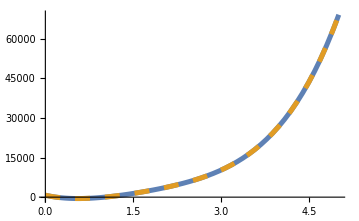
```mathematica
plot2 =Plot[{y3,y4}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
-Graphics-
```

```mathematica
task2 = Table[{x,(31+45x+97Sin[x]+76Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
{{0.,106.0990207889236},{0.25,129.05899776277198},{0.5,173.37405937828655},{0.75,171.99755242601776},{1.,206.46444177554162},{1.25,219.00574843044913},{1.5,214.1289578940995},{1.75,175.4672479550948},{2.,175.00762042545279},{2.25,163.4816807386051},{2.5,131.21034068196806},{2.75,119.16091681914195},{3.,106.89352516936124},{3.25,85.24198223022942},{3.5,87.02941034552407},{3.75,82.40276913114977},{4.,83.6262997063042},{4.25,94.56832099998266},{4.5,112.01887019270842},{4.75,149.79480955363712},{5.,167.55413918567794}}
```

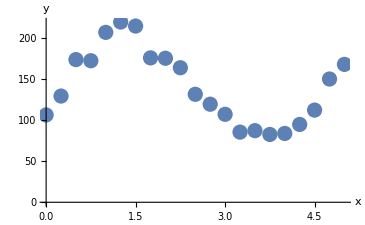
```mathematica
task2Plot=ListPlot[task2, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
-Graphics-
```

```mathematica
y1=Fit[task2, {1,x,Cos[x], Sin[x]},x]
31.37484027359266+43.67485378496187 x+73.73916857609298 Cos[x]+99.46376494772139 Sin[x]
```

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4},x]
94.81688375663896+212.3750991785782 x-124.16318584382091 x^2+20.03691933620372 x^3-0.61007128995495 x^4
```

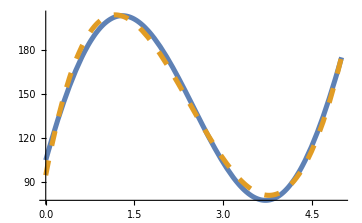
```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
-Graphics-
```

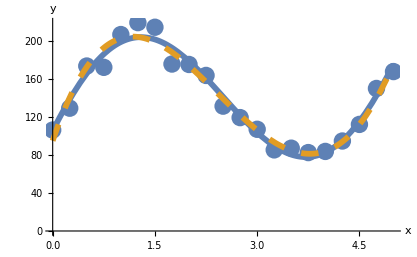
```mathematica
Show[task2Plot, plot2]
-Graphics-
```